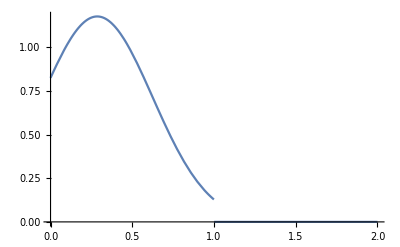

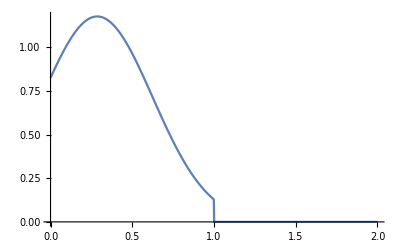

histvecth.csv

xvecth.csv

```mathematica
Clear["Global`*"];
(*Solving for the delta *)
r = 1.4;
sigma = 0.8;
start = (1-1/r)^2 +0.1;
sol = FindRoot[(ⅇ^(-(-1+1/r)^2/(2 q sigma^2)) √q (-1+r) r sigma-ⅇ^(-1/(2 q r^2 sigma^2)) √q r (-1+2 r) sigma-√(π/2) (1+r (-2+r+q r sigma^2)) Erf[(-1+1/r)/(√2 √q sigma)]+√(π/2) (1+r (-2+r+q r sigma^2)) Erf[1/(√2 √q r sigma)])/(√(2 π) r^2)+1/2 Erfc[1/(√2 √q r sigma)]==q,{q, start}];

q0 = q/.sol;

f[x_]:= 1/Sqrt[2Pi q0 sigma^2] Exp[-(x-(1-1/r))^2/(2sigma^2q0)]HeavisideTheta[1-x] ;


Plot[f[x], {x, 0,2}]
xmin = 0;
xmax = 2;
numx = 1000;
xvec = Table[x,{x,xmin,xmax,(xmax-xmin)/(numx-1)}];
histvec = f[xvec];
ListLinePlot[Transpose[{xvec,histvec}],PlotRange->All]

SetDirectory[NotebookDirectory[]];
Export["histvecth.csv",N[histvec]]
Export["xvecth.csv",N[xvec]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in myx near {myx} = {0.9989863715896939353432182340242206919356249272823333740234375}. NIntegrate obtained 96115.7 and 74633.4 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in myx near {myx} = {0.993079210556987}. NIntegrate obtained 161042. and 156844. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in myx near {myx} = {0.986877196163394}. NIntegrate obtained 258339. and 255024. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

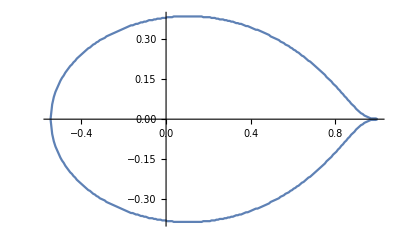

xvecjaccutoff.csv

yvecjaccutoff.csv

yvecellipse.csv

xvecellipse.csv

```mathematica
Clear["Global`*"];

r =1.4;
sigma =0.8;
start = (1-1/r)^2+0.1;
sol = FindRoot[(ⅇ^(-(-1+1/r)^2/(2 q sigma^2)) √q (-1+r) r sigma-ⅇ^(-1/(2 q r^2 sigma^2)) √q r (-1+2 r) sigma-√(π/2) (1+r (-2+r+q r sigma^2)) Erf[(-1+1/r)/(√2 √q sigma)]+√(π/2) (1+r (-2+r+q r sigma^2)) Erf[1/(√2 √q r sigma)])/(√(2 π) r^2)+1/2 Erfc[1/(√2 √q r sigma)]==q,{q, start}];

q0 = q/.sol;

eps = 0.001;
numom = 1000;
ommin = -0.99; 
ommax = 1-r-eps;
omvec = Table[myom,{myom, ommin, ommax, (ommax - ommin)/(numom -1)}];
fvec = Table[0,{myom, ommin, ommax, (ommax - ommin)/(numom -1)}];

For[j= 1, j<numom+1, j++,
om= omvec[[j]];

fvec[[j]] = NIntegrate[sigma^2 Exp[-(myx-(1-1/r ))^2/(2 sigma^2 q0)]/Sqrt[2 Pi sigma^2 q0] r^2myx^2/((1 - r myx - om)^2),{myx, 0, 1}];

];
nearest = Nearest[fvec,1][[1]];
pos = Position[fvec, nearest][[1,1]];
critom= omvec[[pos]];


xmin = critom-0.001;
xmax =1.0;
numx = 200;
xvec = Table[s, {s, xmin, xmax, (xmax-xmin)/(numx-1)}];
crityvec = Table[s,{s, xmin, xmax, (xmax-xmin)/(numx-1)}];
crityvecapprox = Table[s,{s, xmin, xmax, (xmax-xmin)/(numx-1)}];
numy = 200;
ymin = 0; 
ymax =0.55;
yvec = Table[y,{y,ymin, ymax, (ymax - ymin)/(numy -1)}];





effinf  =1000;
eps = 0.0000001;
phi1 =(√q0 sigma (-1+√q0 √(1/(q0 sigma^2)) sigma+Erfc[1/(√2 √q0 r sigma)]))/(2 √(q0 sigma^2));
Monitor[For[j= 1, j<numx+1, j++,
x = xvec[[j]];
fvec = Table[y,{y,ymin, ymax, (ymax - ymin)/(numy -1)}];
fvecapprox = Table[y,{y,ymin, ymax, (ymax - ymin)/(numy -1)}];
For[i = 1, i<numy+1, i++,
y = yvec[[i]];

start =10.0;



fvec[[i]] = NIntegrate[sigma^2 Exp[-(myx-(1-1/r ))^2/(2 sigma^2 q0)]/Sqrt[2 Pi sigma^2 q0] r^2myx^2/((1 - r myx - x)^2+y^2),{myx, 0, 1}];(* +  phi1 r^2sigma^2/((1 - r - x)^2+y^2);*)


];
nearest = Nearest[fvec,1][[1]];
pos = Position[fvec, nearest][[1,1]];
crityvec[[j]] = yvec[[pos]];
];,j];


plt1 = ListLinePlot[Transpose[{ xvec,crityvec}], PlotRange->All];
plt2 = ListLinePlot[Transpose[{ xvec,-crityvec}], PlotRange->All];
Show[plt2, plt1, PlotRange->All]
SetDirectory[NotebookDirectory[]];
Export["xvecjaccutoff.csv", xvec]
Export["yvecjaccutoff.csv", crityvec]

phi = NIntegrate[ Exp[-(myx-(1-1/r ))^2/(2 sigma^2 q0)]/Sqrt[2 Pi sigma^2 q0] ,{myx, 0, 1}];
xmin = -Sqrt[phi sigma^2];
xmax =Sqrt[phi sigma^2];
numx = 1000;
xvec = Table[s, {s, xmin, xmax, (xmax-xmin)/(numx-1)}];
yvecellipse = Sqrt[sigma^2 phi-xvec^2];
Export["yvecellipse.csv", yvecellipse]
Export["xvecellipse.csv", xvec]
```